## Drell-Yan

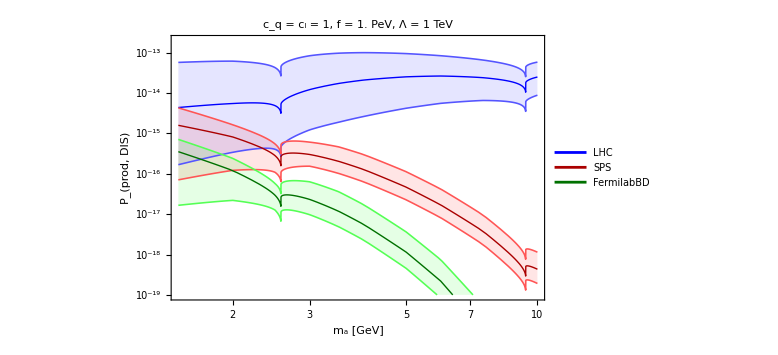

C:\Users\miksi\Dropbox\Science 2\HNL and scalar phenomenology\ALP phenomenology\Temp\plots\DIS-production-uncertainty.pdf

```mathematica
σDrellYanDataALPFromGluonTemp["FermilabBD"]=Import[FileNameJoin[{NotebookDirectory[]//ParentDirectory//ParentDirectory,"phenomenology/ALPs with gluon coupling/branching ratios/sigma-prod-ALP-gluon-Drell-Yan-FNAL.txt"}],"Table"];
σDrellYanDataALPFromGluonTemp["SPS"]=Import[FileNameJoin[{NotebookDirectory[]//ParentDirectory//ParentDirectory,"phenomenology/ALPs with gluon coupling/branching ratios/sigma-prod-ALP-gluon-Drell-Yan-SPS.txt"}],"Table"];
σDrellYanDataALPFromGluonTemp["LHC"]=Import[FileNameJoin[{NotebookDirectory[]//ParentDirectory//ParentDirectory,"phenomenology/ALPs with gluon coupling/branching ratios/sigma-prod-ALP-gluon-Drell-Yan-LHC.txt"}],"Table"];
{σppFacility["FermilabBD"],σppFacility["SPS"],σppFacility["LHC"]}={40*10^9*12^-0.29,40*10^9*96^-0.29,78*10^9};
Do[
cGval[ma_,model,Λ_]=(cG+cGGeff[ma,cu,cd,cs,cc,cb,ct,{"u","d","s","c","b","t"}])/.tableValuesReplacement[model,Λ];
Do[
PALPprod["Drell-Yan",model,facility,ma_,f_,Λ_]=If[ma>=1.5,Evaluate[1/σppFacility[facility] 1/f^2 Abs[cGval[ma,model,Λ]]^2 10^(Interpolation[Log10[σDrellYanDataALPFromGluonTemp[facility][[All,{1,2}]]],InterpolationOrder->1][Log10[ma]])],0];
PALPprodLower["Drell-Yan",model,facility,ma_,f_,Λ_]=If[ma>=1.5,Evaluate[1/σppFacility[facility] 1/f^2 Abs[cGval[ma,model,Λ]]^2 10^(Interpolation[Log10[σDrellYanDataALPFromGluonTemp[facility][[All,{1,3}]]],InterpolationOrder->1][Log10[ma]])],0];
PALPprodUpper["Drell-Yan",model,facility,ma_,f_,Λ_]=If[ma>=1.5,Evaluate[1/σppFacility[facility] 1/f^2 Abs[cGval[ma,model,Λ]]^2 10^(Interpolation[Log10[σDrellYanDataALPFromGluonTemp[facility][[All,{1,4}]]],InterpolationOrder->1][Log10[ma]])],0];
,{facility,listFacility}]
,{model,ModelListAll}];
fval=10^6.;
DISuncertainty=Show[LogLogPlot[{PALPprod["Drell-Yan","Fermion universal","LHC",ma,fval,10^3],PALPprodLower["Drell-Yan","Fermion universal","LHC",ma,fval,10^3],PALPprodUpper["Drell-Yan","Fermion universal","LHC",ma,fval,10^3],PALPprod["Drell-Yan","Fermion universal","SPS",ma,fval,10^3],PALPprodLower["Drell-Yan","Fermion universal","SPS",ma,fval,10^3],PALPprodUpper["Drell-Yan","Fermion universal","SPS",ma,fval,10^3],PALPprod["Drell-Yan","Fermion universal","FermilabBD",ma,fval,10^3],PALPprodLower["Drell-Yan","Fermion universal","FermilabBD",ma,fval,10^3],PALPprodUpper["Drell-Yan","Fermion universal","FermilabBD",ma,fval,10^3]},{ma,1.5,10},PlotStyle->{{Thick,Blue},{Thickness[0.002],Lighter@Blue},{Thickness[0.002],Lighter@Blue},{Thick,Darker@Red},{Thickness[0.002],Lighter@Red},{Thickness[0.002],Lighter@Red},{Thick,Darker@Darker@Green},{Thickness[0.002],Lighter@Green},{Thickness[0.002],Lighter@Green},{Thick,Cyan},{Thick,Magenta},{Thick,Purple},{Thick,Black,Dashing[0.02]},{Thick,Blue},{Thickness[0.003],Gray,Dashing[0.01]},{Thick, Darker@Red,Dashing[0.02]},{Thick,Darker@Darker@Green,Dashing[0.02]},{Thick,Orange,Dashing[0.02]},{Thick,Cyan,Dashing[0.02]},{Thick,Magenta,Dashing[0.02]},{Thick,Purple,Dashing[0.02]},{Thick,Blue,Dashing[0.02]},{Thick,Darker@Cyan,Dashing[0.02]}},Frame-> True,FrameLabel->{"m_a [GeV]" , "P_(prod, DIS)"},FrameStyle->Directive[Black, 23],ImageSize->Large,PlotRange->{{1.5,10},{(10^3/fval)^2 10^-13,(10^3/fval)^2 2*10^-7}},Filling->{2->{{3},Directive[Blue,Opacity[0.1]]},5->{{6},Directive[Red,Opacity[0.1]]},8->{{9},Directive[Green,Opacity[0.1]]}},PlotLabel->Style[Row[{"c_q = c_l = 1, f = "<>ToString[10^-6. fval]<>" PeV, Λ = 1 TeV"}],22,Black]],LogLogPlot[{x,x^2,x^3},{x,1.5,10},PlotStyle->{{Thick,Blue},{Thick,Darker@Red},{Thick,Darker@Darker@Green}},PlotLegends->Placed[Style[#,20]&/@Join[{"LHC","SPS","FermilabBD"}],{0.13,0.2}]]]
Export[FileNameJoin[{NotebookDirectory[]//ParentDirectory//ParentDirectory,"plots/DIS-production-uncertainty.pdf"}],DISuncertainty]
```